# Vertical Lattice Calculations

## Define Params:

Physical Constants:

```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .52*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;
```

Strontium Properties:

```mathematica
λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 300*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency, clock trans ??? *)
```

Beam Parameters, and some rough estimates of depth:

```mathematica
who = 50*10^-6
θ = 40*π/180; (* full angle between the two beams *)
wvert = who*Sin[θ/2]//N
λp = λ813/(2 Sin[θ/2]); (* effective lattice spacing *)
Plattice = .4; (* Incident power per beam *)
Ulattice = (α 4 Plattice)/(ϵ0 c π wvert*who);
TrapDepthuK = 10^6 Ulattice/kB;
TrapDepthHz = 1/(2π)Ulattice/ℏ;
ωtrap = 2π 1/λp √((2*Ulattice)/m);

TableForm[{θ*180/π, λp*10^6, Plattice*1000, TrapDepthuK, TrapDepthHz/1000, ωtrap/(2000π)}, TableHeadings -> {{"Total Beam Separation Angle (degrees)","Lattice Spacing (μm)", "Power Per beam (mW)", "Trap Depth (uK)","Trap Depth (kHz)", "Longitudinal Frequency (kHz)"}}]
```

1/20000

0.000017101

Total Beam Separation Angle (degrees) | 40
Lattice Spacing (μm) | 1.18911
Power Per beam (mW) | 400.
Trap Depth (uK) | 80.429
Trap Depth (kHz) | 1675.08
Longitudinal Frequency (kHz) | 104.262

## What should spot size be to get desired waist?

The initial size of the two beams sets how tightly they will get focused when they overlap.  Figure out for a given focal length of lens, how small the spot will be.

```mathematica
f1 = 0.03;
spotsep = 2*f1*Sin[θ/2];
w0 = .4*10^-3;
zr0 = (π w0^2)/λ813;
({{am, bm}, {cm, dm}})= ({{1, f1}, {0, 1}}).({{1, 0}, {-1/f1, 1}});
q1inv = - (ⅈ λ813)/(π w0^2);
q2inv = (cm + dm*q1inv)/(am + bm*q1inv);
w2 = Simplify[√(-λ813/(π Im[q2inv]))]; (* waist at the focus of the lenses *)
zr2 = (π w2^2)/λ813;
hoproj = w2/Sin[θ/2]; (*in terms of diameter*)
TableForm[{f1*100, spotsep*100, w0*10^6, zr0, zr2, w2*10^6, hoproj*10^6}, TableHeadings -> {{"focal length (cm)", "spot separation (cm)","waist at lens (μm)", "Rayleigh Range prior to lens (m)", "Rayleigh Range after lens (m)", "Waist at focus (μm)", "Horizontal projection at focus, waist (μm)"}}]
```

focal length (cm) | 3.
spot separation (cm) | 2.05212
waist at lens (μm) | 400.
Rayleigh Range prior to lens (m) | 0.617968
Rayleigh Range after lens (m) | 0.00145639
Waist at focus (μm) | 19.4185
Horizontal projection at focus, waist (μm) | 56.7759

## What about in the horizontal direction?

The initial size of the two beams sets how tightly they will get focused when they overlap.  Figure out for a given focal length of lens, how small the spot will be.

```mathematica
fh = 0.03;
w0 = .13*10^-3;
zr0 = (π w0^2)/λ813;
({{am, bm}, {cm, dm}})= ({{1, fh}, {0, 1}}).({{1, 0}, {-1/fh, 1}});
q1inv = - (ⅈ λ813)/(π w0^2);
q2inv = (cm + dm*q1inv)/(am + bm*q1inv);
w2h = Simplify[√(-λ813/(π Im[q2inv]))]; (* waist at the focus of the lenses *)
zr2 = (π w2h^2)/λ813;

TableForm[{fh*100, w0*10^6, zr0, zr2, w2h*10^6}, TableHeadings -> {{"focal length (cm)","waist at lens (μm)", "Rayleigh Range prior to lens (m)", "Rayleigh Range after lens (m)", "Waist at focus (μm)"}}]
```

focal length (cm) | 3.
waist at lens (μm) | 130.
Rayleigh Range prior to lens (m) | 0.0652728
Rayleigh Range after lens (m) | 0.0137883
Waist at focus (μm) | 59.7492

## Other two beams -- what lenses to get reasonable waist?

These lenses will have to be a

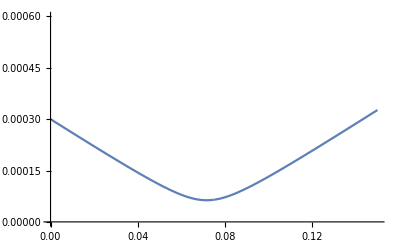

focal length (cm) | 7.5
waist at lens (μm) | 300.
Rayleigh Range prior to lens (m) | 0.347607
Rayleigh Range after lens (cm) | 1.61821
Waist at focus (μm) | 64.7283

```mathematica
f = 0.075;
w0 = .3*10^-3;
zr0 = (π w0^2)/λ813;
({{am, bm}, {cm, dm}})= ({{1, z}, {0, 1}}).({{1, 0}, {-1/f, 1}});
q1inv = - (ⅈ λ813)/(π w0^2);
q2inv = (cm + dm*q1inv)/(am + bm*q1inv);
w2h = Simplify[√(-λ813/(π Im[q2inv]))]; (* waist at the focus of the lenses *)
zr2 = (π w2h^2)/λ813;
Plot[w2h, {z, 0, 2*f}, PlotRange->{0, 2w0}]

TableForm[{f*100, w0*10^6/.z->f, zr0/.z->f, zr2*10^2/.z->f, w2h*10^6/.z->f}, TableHeadings -> {{"focal length (cm)","waist at lens (μm)", "Rayleigh Range prior to lens (m)", "Rayleigh Range after lens (cm)", "Waist at focus (μm)"}}]
```

## Tunneling rates and inhomogs

The initial size of the two beams sets how tightly they will get focused when they overlap.  Figure out for a given focal length of lens, how small the spot will be.

```mathematica
w = 100*10^-6;
Ulattice = 3.5*10^-30;
λlat = λ813 √2;
klat =(2π)/λlat;
Erec = ℏ^2 klat^2/(2m);
TrapDepthErec = Ulattice/Erec;
TrapDepthHz = 1/(2π)Ulattice/ℏ;
JHz = 4/(2 π^2 ℏ)Erec (Ulattice/Erec)^(3/4)Exp[-2(Ulattice/Erec)^(.5)];(* from https://journals.aps.org/rmp/abstract/10.1103/RevModPhys.80.885 *)
sol = Solve[1-JHz/TrapDepthHz== Exp[-x^2/w^2]/.z->f, x][[2]];
Jexact3Erec = 0.444/4 Erec/(2π ℏ);
Jexact5Erec = 0.263/4 Erec/(2π ℏ);

HomogSites = 2(x/.sol)/λlat; (* this should be the number of sites along a direction *)
TableForm[{TrapDepthHz, TrapDepthErec, JHz, HomogSites}, TableHeadings -> {{"Trap Depth (Hz)","Lattice Depth (Erec)", "Tunneling Rate (Hz)", "Number of sites within J of max depth"}}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Trap Depth (Hz) | 5282.17
Lattice Depth (Erec) | 3.04686
Tunneling Rate (Hz) | 155.102
Number of sites within J of max depth | 30.0152

```mathematica
ℏ(2π/λ689)^2/(2π 2m)
```

4832.37

```mathematica
m
```

1.4442×10^-25